```mathematica
pivots[A_]:=Flatten[FirstPosition[1]/@Transpose[A]]
```

```mathematica
pMatrix[n_]:=Table[
Which[i==2&&j==1||i==1&&j==2,-1/2,
i==j&&i>2,1,
True,0],{i, n},{j,n}]
```

```mathematica
gramMatrix[W_]:=Simplify[Transpose[W].pMatrix[Length[W]].W]
```

```mathematica
linearRelationsMatrix[G_]:=RowReduce[G][[1;;MatrixRank[G]]]//Transpose
```

```mathematica
linearRelations[L_]:=Select[
Table[Equal[Subscript[b, i],L[[i]].Table[Subscript[b, i],{i,pivots[L]}]],{i,Length[L]}],Not[BooleanQ[#]]&]
```

```mathematica
linearRelationsFromW=linearRelations@*linearRelationsMatrix@*gramMatrix;
```

```mathematica
inverseLinearRelations[G_]:=Table[If[i==#,1,0],{i,Length[G[[1]]]}]&/@Flatten[FirstPosition[#,1]&/@(RowReduce[G]//Select[Not[AllTrue[#,#==0&]]&])]
```

```mathematica
quadraticFormMatrix[G_,L_]:=Inverse[Table[G[[i, j]],{i,pivots[L]},{j,pivots[L]}]]
```

```mathematica
quadraticForm[Q_,L_]:=Module[{v=Table[Subscript[b, i],{i,pivots[L]}]},Simplify[v.Q.v==0]]
```

```mathematica
quadform[W_]:=Module[{G=gramMatrix[W]},Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]]
```

```mathematica
quadformFromG[G_]:=Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]
```

```mathematica
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];
```

```mathematica
FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,orderings,pAdj,rightF,s,t,initial,face},m=AdjacencyMatrix[g];
Table[pAdj[v]=SortBy[Pick[VertexList[g],m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,VertexList[g]}];
rightF[_]:=False;
Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,EdgeList[g]}]][[2,1]]]
```

```mathematica
findGenerators[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@Solve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsFromG[G_]:=findGenerators[FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]],Range[Length[G]],G]
```

```mathematica
root={-1,2,2,4,4}
```

{-1,2,2,4,4}

```mathematica
faces=FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]]
```

{{1,2,4},{1,3,2},{1,4,5},{1,5,3},{2,3,6},{2,6,4},{3,5,6},{4,6,5}}

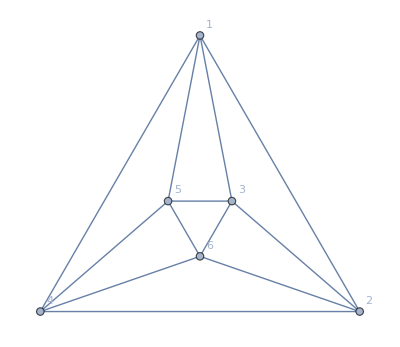

```mathematica
PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
G={{1,-1,-1,-1,-1,-3},{-1,1,-1,-1,-3,-1},{-1,-1,1,-3,-1,-1},{-1,-1,-3,1,-1,-1},{-1,-3,-1,-1,1,-1},{-3,-1,-1,-1,-1,1}}
```

{{1,-1,-1,-1,-1,-3},{-1,1,-1,-1,-3,-1},{-1,-1,1,-3,-1,-1},{-1,-1,-3,1,-1,-1},{-1,-3,-1,-1,1,-1},{-3,-1,-1,-1,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[G]
```

{{{1,0,0,0,0,0},{0,1,0,0,0,0},{3,4,0,3,0,-1},{0,0,0,1,0,0},{3,3,0,4,0,-1},{2,4,0,4,0,-1}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{3,4,3,0,0,-1},{3,3,4,0,0,-1},{2,4,4,0,0,-1}},{{1,0,0,0,0,0},{4,0,-1,3,3,0},{4,0,-1,2,4,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{3,0,-1,3,4,0}},{{1,0,0,0,0,0},{4,0,3,-1,3,0},{0,0,1,0,0,0},{4,0,2,-1,4,0},{0,0,0,0,1,0},{3,0,3,-1,4,0}},{{-1,4,4,0,0,2},{0,1,0,0,0,0},{0,0,1,0,0,0},{-1,4,3,0,0,3},{-1,3,4,0,0,3},{0,0,0,0,0,1}},{{0,4,-1,3,0,3},{0,1,0,0,0,0},{0,4,-1,2,0,4},{0,0,0,1,0,0},{0,3,-1,3,0,4},{0,0,0,0,0,1}},{{0,0,3,-1,4,3},{0,0,3,-1,3,4},{0,0,1,0,0,0},{0,0,2,-1,4,4},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{-1,0,0,4,4,2},{-1,0,0,4,3,3},{-1,0,0,3,4,3},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}}

```mathematica
search[generators_,current_,previous_,lastgen_,upperBound_,faces_]:=Block[{totals,invalid},
Print[current];
invalid[σ_,face_]:=σ==lastgen||AllTrue[Delete[σ.current,{#}&/@face],#>upperBound&];
totals[i_]:=If[invalid[generators[[i]],faces[[i]]],0,
Length[current]-Length[faces[[i]]]-Length[Select[Delete[current,{#}&/@faces[[i]]],#>upperBound&]]+search[generators,generators[[i]].current,current,generators[[i]],upperBound,faces]];
Total[totals/@Range[Length[generators]]]]
```

```mathematica
sigmas[[2]].sigmas[[1]].{-1,2,2,4,4,7}
```

{-1,2,10,20,28,31}